# Assignment 8 Example Solutions

This is an example solution set for assignment #8, Caltech BE/CS 191a, Winter 2022.   Prof. Erik Winfree <winfree@caltech.edu>
Do not share this with anyone who is not currently taking the class.
And to state the obvious, do not look at this notebook if you have not yet turned in assignment #8.

To load relevant simulator code, you must start by opening and executing the initialization cells in SurfaceCRNs.nb

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorSSA.m"]
Get["CRNSimulatorExtensions.m"]
```

## Part 1: Well-mixed and surface CRNs that solve graph coloring problems by stochastic local search.

(a).  Given k>1 and an arbitrary connected graph G=(V,E), construct a well-mixed stochastic CRN that is guaranteed to halt with a solution to the k-coloring problem if one exists (and will run forever otherwise).   The graph G has vertices V and undirected edges E.  A k-coloring is a map from V to {1,..., k} such that no two adjacent vertices have the same color.  Four example graphs are given; the example coloring for G1 is valid, the example coloring for G2 is invalid,  the randomly-chosen one for G3 is probably invalid, and the example coloring for G4 is valid.  Your CRN should have no more than O(k|E|) reactions.  Feel free to demonstrate success on graphs other than the ones below.

Technical note:  I encountered a bug when using Table[ ] and Do[ ] with graphs where the vertices are represented as symbols.  So I advise representing vertices as either integers or strings.

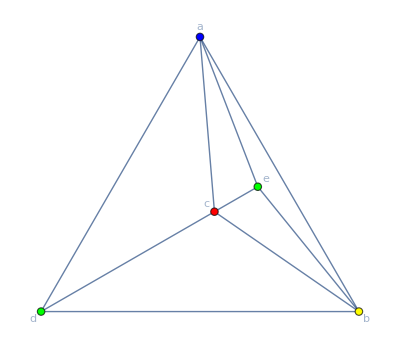

```mathematica
G1 = Graph[{"a","b","c","d","e"},{"a"<->"b","a"<->"c","a"<->"d","a"<->"e","b"<->"c","b"<->"d","b"<->"e","c"<->"d","c"<->"e"}];
PlanarGraph[G1,VertexLabels->Automatic,VertexStyle->{"a"->Blue,"b"->Yellow,"c"->Red,"d"->Green,"e"->Green}]
```

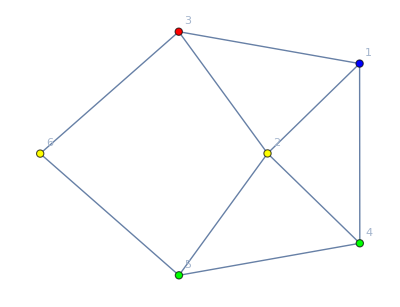

```mathematica
G2=Graph[{1,2,3,4,5,6},{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->6,4<->5,5<->6}];
Graph[G2,VertexLabels->Automatic,VertexStyle->{1->Blue,2->Yellow,3->Red,4->Green,5->Green,6->Yellow}]
```

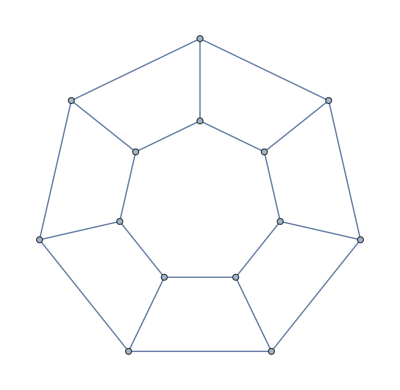

```mathematica
G3=PetersenGraph[7,6]
```

```mathematica
{VertexList[G3],EdgeList[G3]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1<->2,1<->7,1<->8,2<->3,2<->9,3<->4,3<->10,4<->5,4<->11,5<->6,5<->12,6<->7,6<->13,7<->14,8<->9,8<->14,9<->10,10<->11,11<->12,12<->13,13<->14}}

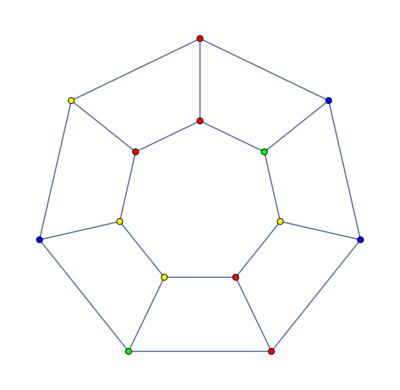

```mathematica
Graph[G3,VertexStyle->(MapThread[Rule,{Range[14],RandomChoice[{Red,Green,Blue,Yellow},14]}])]
```

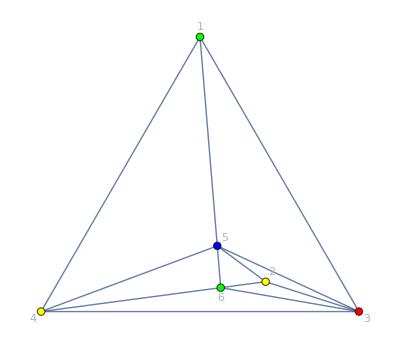

```mathematica
G4 = Graph[{1,2,3,4,5,6},{1<->4,1<->3,4<->3,5<->3,6<->3,4<->5,5<->6,2<->6,3<->2,4<->6,1<->5,2<->5}];
PlanarGraph[G4,VertexLabels->Automatic,VertexStyle->{1->Green,2->Yellow,3->Red,4->Yellow,5->Blue,6->Green}]
```

Here is a well-mixed CRN.   Let the n=|V| vertices be numbered 1...n.  The initial state will consist of 1 molecule each, V[v] for each vertex 1≤v≤n, indicating that they have no guess about their color yet.  The basic idea is that the vertices will proceed to guess colors at random, sticking to their guess until a contradiction is observed, in which case both of the vertices involved in the conflict will change its color randomly. (We only need one to do so, but either one must be able to change, because we don’t know which one needs to be recolored.)  When there are no conflicts remaining, there will also be no further reactions that can occur.  Further, we know that from any current coloring, it is possible to find a correct coloring if a valid coloring exists, so the CRN won’t get stuck: with each conflict, at least one vertex disagrees with a reference valid coloring, and that vertex could be chosen to change to its correct color while the other vertex perhaps doesn’t change.  So we have a sequence of events that consistently decreases the deviation from the reference coloring until either the reference coloring is obtained, or another coloring is obtained that has no conflicts.  Call this the reference trajectory from the given state.  Also note that for any state representing an invalid coloring, there is some finite, fixed probability of subsequently following the reference trajectory to a valid coloring; let ϵ be the smallest such probability.  Then from any invalid-coloring state, there is a probability p≥ϵ that the reference trajectory is subsequently followed all the way, and thus a probability q≤ϵ that the subsequent trajectory eventually makes a first deviation from the reference trajectory (perhaps discovering a non-reference valid coloring, perhaps not).  Thus, the probability that after N deviations from reference trajectories, a valid coloring is still not achieved, is less than (1-ϵ)^N, which goes to zero.  Since there are a finite number of states in the system, and thus a reference trajectory (which can’t repeat itself) has bounded length, deviations accumulate at least linearly in time, and thus the probability of not finding a solution decreases exponentially in time.  Granted, ϵ might be very small for some graphs, so the CRN could still take exponential time to complete, but we know that the probability it hasn’t completed yet goes to zero -- it won’t get stuck in loops or deadlocks.

Our CRN has |V|(k+1) species and  (|V| + |E|)k reactions.

```mathematica
ColoringCRN[G_,k_]:=Flatten[Join[
Table[rxn[V[v],V[v,c],1],{v,VertexList[G]},{c,Range[k]}],  (* a vertex without a color will randomly choose a color *)Table[rxn[V[First[e],c]+V[Last[e],c],V[First[e]]+V[Last[e]],1],{e,EdgeList[G]},{c,Range[k]}], (* conflicting edges recolor *)
Table[conc[V[v],1],{v,VertexList[G]}] (* each vertex starts uncolored *)
]]
```

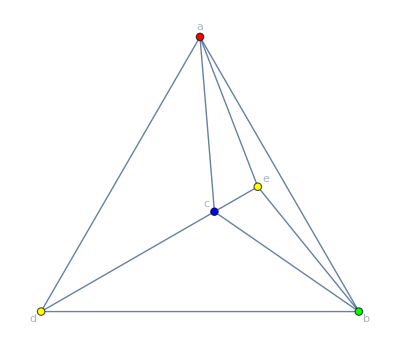

```mathematica
rsys=ColoringCRN[G1,4];
trajectory=SimulateRxnsysSSA[rsys,Infinity];
PlanarGraph[G1,VertexLabels->Automatic,VertexStyle-> 
Cases[ MapThread[Rule,{SpeciesInRxnsys[rsys],Last[trajectory["Values"]]}], (V[v_,c_]->1):>(v->{Red,Green,Blue,Yellow}[[c]]) ]]
```

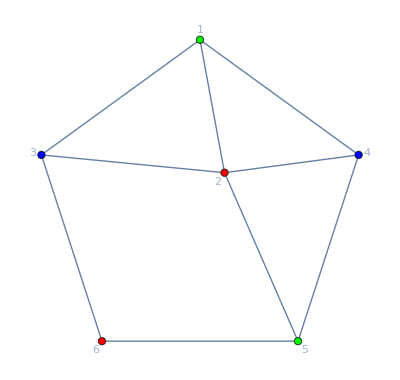

```mathematica
rsys=ColoringCRN[G2,3];
trajectory=SimulateRxnsysSSA[rsys,Infinity];
PlanarGraph[G2,VertexLabels->Automatic,VertexStyle-> 
Cases[ MapThread[Rule,{SpeciesInRxnsys[rsys],Last[trajectory["Values"]]}], (V[v_,c_]->1):>(v->{Red,Green,Blue,Yellow}[[c]]) ]]
```

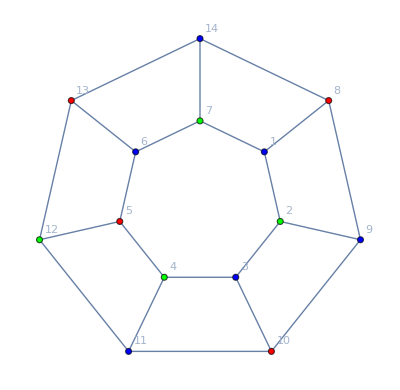

```mathematica
rsys=ColoringCRN[G3,3];
trajectory=SimulateRxnsysSSA[rsys,Infinity];
PlanarGraph[G3,VertexLabels->Automatic,VertexStyle-> 
Cases[ MapThread[Rule,{SpeciesInRxnsys[rsys],Last[trajectory["Values"]]}], (V[v_,c_]->1):>(v->{Red,Green,Blue,Yellow}[[c]]) ]]
```

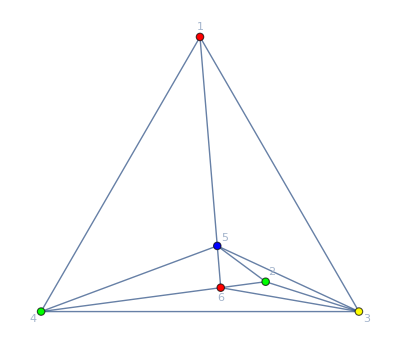

```mathematica
rsys=ColoringCRN[G4,4];
trajectory=SimulateRxnsysSSA[rsys,Infinity];
PlanarGraph[G4,VertexLabels->Automatic,VertexStyle-> 
Cases[ MapThread[Rule,{SpeciesInRxnsys[rsys],Last[trajectory["Values"]]}], (V[v_,c_]->1):>(v->{Red,Green,Blue,Yellow}[[c]]) ]]
```

```mathematica
(* watch it search for the solution *)
ArrayPlot[trajectory["Values"]]
```

-Graphics-

(b).  Construct a single surface CRN that finds a 4-coloring for an arbitrary planar graph.   That is, the graph will be provided already encoded in the initial layout in a straightforward manner, and the surface CRN will eventually establish a color for each vertex and halt, with no more reactions possible.  We need to be clear about what we mean by “encoded in the initial layout” and “establish a color for each vertex”. 

Use the following encoding for the graphs:  Each vertex corresponds to a connected set of sites containing initial species “v”.   Each edge will consist of exactly 2 adjacent “e” sites, incident to each vertex region at exactly 1 site each, and not touching any other edge or vertex.  Unoccupied sites will be “w”.  Example layouts are given for G1, G2, G3, G4 from above.   To color a vertex region, the “v” species -- all of them! -- must be changed to a species indicating the color, e.g. “v[R]”, “v[G]”, “v[B]”, “v[Y]”, or if you prefer numbers, “v[1]”, “v[2]”, “v[3]”, “v[4]”.   For a valid coloring, all sites with a given vertex region must be the same color, neighboring vertex regions must have different colors, edge sites can be anything, and unoccupied sites must never change.  Your CRN may introduce additional species as necessary, so long as the system is guaranteed to eventually halt with a valid coloring.  

Relevant background: For planar graphs, the 3-color decision problem (“does there exist a valid 3-coloring?”) is NP-complete, so finding an actual solution is NP-hard, but the 4-color decision problem (“does there exist a valid 4-coloring?”) is trivial because in 1976 Appel & Haken proved that the answer is always “yes!”... but actually finding a valid 4-coloring can still be challenging (see e.g. Heuristics for Rapidly Four-Coloring Large Planar Graphs, Morgenstern & Shapiro, 1991).  The argument for the correctness of your surface CRN (which need not be efficient, just correct) may rely on the assumed correctness of Appel & Haken’s proof.

How would you modify your surface CRN to find solutions to solvable 3-coloring problems or 5-coloring problems?  Non-planar graphs?  What happens if there is no valid coloring?  What might affect how efficiently (quickly) it finds solutions, and could your CRN be modified for greater efficiency?  Please do not actually solve these problems, but just think about them and offer some commentary about how one might approach them.

```mathematica
Clear[w,v,e,R,G,B,Y];
```

```mathematica
mapG1={
{v,v,v,v,v,v,v,v,v,v,v,v,v,v,w},
{v,w,w,v,w,w,w,v,v,v,w,w,w,v,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,v,v,v,w,w,v,v,v,w,w,v,v,v},
{e,w,v,v,v,e,e,v,v,v,e,e,v,v,v},
{e,w,v,v,v,w,w,v,v,v,w,w,v,v,v},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,v,w,w,w,v,v,v,w,w,w,v,w},
{v,v,v,v,v,v,v,v,v,v,v,v,v,v,w}
};
```

```mathematica
mapG2={
{w,w,w,w,w,w,w,w,w,w,w,w,w,w},
{w,v,v,v,v,v,e,e,v,v,v,v,v,w},
{w,v,v,v,v,w,w,w,v,v,v,w,e,w},
{w,v,v,v,e,w,v,w,e,v,w,w,e,w},
{w,e,w,w,e,v,v,v,e,w,w,v,v,w},
{w,e,w,e,v,v,v,w,w,w,v,v,v,w},
{w,v,v,e,w,w,e,e,w,w,v,v,v,w},
{w,v,v,v,e,w,w,v,v,w,e,w,v,w},
{w,v,w,w,e,v,v,v,v,v,e,w,w,w},
{w,w,w,w,w,w,w,w,w,w,w,w,w,w}
};
```

```mathematica
mapG3={
{w,w,w,e,e,v,v,v,v,v,v,v,v,v,v,v,e,e,w,w,w},
{w,v,v,v,w,w,w,w,w,v,v,v,w,w,w,w,w,v,v,v,w},
{w,v,v,v,e,e,w,w,w,w,e,w,w,w,w,e,e,v,v,v,w},
{v,v,v,v,w,v,v,v,w,w,e,w,w,v,v,v,w,v,v,v,v},
{v,w,w,w,w,v,v,v,w,v,v,v,w,v,v,v,w,w,w,w,v},
{v,w,w,w,e,v,v,v,w,v,v,v,w,v,v,v,e,w,w,w,v},
{e,w,w,w,e,w,w,e,e,v,v,v,e,e,w,w,e,w,w,w,e},
{e,w,w,v,v,v,w,w,w,w,w,w,w,w,w,v,v,v,w,w,e},
{v,w,w,v,v,v,v,e,w,w,w,w,w,e,v,v,v,v,w,w,v},
{v,w,e,v,v,v,w,e,w,w,w,w,w,e,w,v,v,v,e,w,v},
{v,v,e,w,w,w,v,v,v,w,w,w,v,v,v,w,w,w,e,v,v},
{v,v,w,w,w,e,v,v,v,v,e,w,v,v,v,e,w,w,w,v,v},
{v,v,e,w,w,e,w,v,v,w,e,v,v,v,w,e,w,w,e,v,v},
{w,w,e,v,v,v,w,w,w,w,w,w,w,w,w,v,v,v,e,w,w},
{w,w,w,v,v,v,v,v,v,e,e,v,v,v,v,v,v,v,w,w,w}
};
```

```mathematica
mapG4={
{v,v,v,v,w,w,v,v,v,v,v,v,v,v,v },
{v,v,v,v,e,e,v,v,v,v,v,v,v,v,v},
{v,v,v,v,w,w,v,v,v,v,v,v,v,v,v},
{e,w,w,e,w,w,e,w,w,w,w,w,w,w,v},
{e,w,w,e,w,w,e,w,w,w,w,w,w,w,v},
{v,e,e,v,v,v,v,e,e,v,v,v,e,e,v},
{v,w,w,v,v,v,v,w,w,v,v,v,w,w,v},
{v,w,w,v,v,v,v,w,w,v,v,v,w,w,v},
{v,w,w,w,w,w,e,w,w,w,e,w,w,w,v},
{v,w,w,w,w,w,e,w,w,w,e,w,w,w,v},
{v,v,v,v,e,e,v,v,v,v,v,v,e,e,v},
{v,v,v,v,w,w,v,v,v,v,v,v,w,w,e},
{v,v,v,v,w,w,v,v,v,v,v,v,w,w,e},
{v,v,v,v,w,w,w,w,w,w,w,w,w,w,v},
{v,v,v,v,v,v,v,v,v,v,v,v,v,v,v}
};
```

Our surface CRN operates on the same principle as the well-mixed CRN: If two neighboring vertices have the same color, they will learn of this result and at least one will choose a new random color; otherwise, neither will not change color.  This dictum is not entirely clear, since each graph vertex corresponds to an entire area on the surface, and we need to break down the operational rules such that they apply to individual pairs of sites on the surface, rather than to whole areas.  So we will state what must be true, pairwise, in a valid solution -- and then create reactions that detect violations and make random choices that (might) fix them.  Finally, to show that the resulting logic guarantees convergence to a valid coloring, we analyze trajectories based on local logical constraints, conserved quantities and reachability to show that a valid coloring can always be reached, if one exists.

Recall that the “map area” associated with a vertex is a (north-east-south-west) connected set of “v” sites, and more good measure we will include one of the adjacent “e” sites for each connecting edge pair.  Now suppose we are attempting a k coloring.  In addition to the initial v, e, and w, we will have species
	v[c] 		for 1≤c≤k to represent the vertex being color c
	e[c]		for 1≤c≤k to represent a signal saying that the immediately adjacent vertex is color c
for a total of 3+2k species and, as given below, 4 k^2-2k reactions to find a k-coloring, independent of which or how large the graph is.

The local logical constraints are:
	adjacent v sites must be the same color (i.e. a single vertex must have its entire map area colored the same)
	edge sites must be the same color as the adjacent map area
	edge sites must NOT be the same color as adjacent edges (which we know belong to a different vertex and map area)
If all these logical constraints are satisfied, then the graph coloring corresponding to the surface CRN state is well defined, and neighboring vertices have different colors, and thus we have a solution to the coloring problem.

To go from these constraints to a stochastic surface CRN, we note that any violation of these constraints can be detected by a pair of sites.  See the code below for the exact reactions, or imagine them here based on the constraints above.  Most importantly, a surface state that satisfies all these constraints by definition corresponds to a valid coloring and no further reactions will be possible; conversely, for any valid coloring there exists a corresponding surface state.

The main conserved quantity is that the the v/e/w aspect of each surface site never changes, only the coloring on top of it changes.  The reachability statements are twofold: First, from ANY state preserving the conserved quantity, we can reach a state in which each map area (v and e sites both) is colored with a single color.  This should be obvious how to achieve.  Second, given any state in which each map area has a uniform color, and for any reaction that could take place in the corresponding state of the well-mixed coloring CRN of part (a) of this homework, the surface CRN can re-color just one map area in the same corresponding way (i.e. that state is reachable).  Now, combined with the correctness of the well-mixed CRN, we have shown the correctness of the surface CRN -- if a valid coloring exists, then it is possible for the surface CRN to discover it, and since there are finitely many states to reach, eventually it will do so.

General version of the surface CRN, for any number of colors:

```mathematica
surfacecolor[k_]:=Flatten[{
Table[{rxno[v,v[c],1],rxno[e,e[c],1]},{c,1,k}],(* uncolored sites choose random colors *)
Table[If[c1=!=c2,
{ 
rxno[v[c1]+v[c2],v[c2]+v[c2],1],(* neighboring v must agree; if not, one randomly follows the other *)
rxno[v[c1]+e[c2],v[c1]+e[c1],1],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxno[v[c1]+e[c2],v[c2]+e[c2],1],
rxno[e[c1]+e[c1],e[c1]+e[c2],1] (* adjacent edge sites must be different; if not, one randomly changes *)
},
{}],
{c1,1,k},{c2,1,k}]
}]
mapcoloring[k_]:=With[{colors=ColorData["Rainbow"]/@Range[0,1,1/(k-1)]},
Flatten[Join[
{w->White,v->Gray,e-> Black},
Table[{v[i]->colors[[i]],e[i]->Lighter[colors[[i]]]},{i,1,k}]
]]]
```

```mathematica
Length[surfacecolor[4]]
```

56

```mathematica
Dynamic[ArrayPlot[solidmap,ColorRules->solidcolors,PlotLabel->solidtime]]
```

```mathematica
solidmap=mapG1;solidCRN=surfacecolor[4];solidcolors=mapcoloring[4];solidtime=0;
While[!HaltedSurfaceCRNQ[solidCRN,solidmap],solidmap=RunSurfaceCRN[solidCRN,solidmap,1];solidtime+=1]
```

```mathematica
solidmap=mapG2;solidCRN=surfacecolor[3];solidcolors=mapcoloring[3];solidtime=0;
While[!HaltedSurfaceCRNQ[solidCRN,solidmap],solidmap=RunSurfaceCRN[solidCRN,solidmap,1];solidtime+=1]
```

```mathematica
solidmap=mapG3;solidCRN=surfacecolor[3];solidcolors=mapcoloring[3];solidtime=0;
While[!HaltedSurfaceCRNQ[solidCRN,solidmap],solidmap=RunSurfaceCRN[solidCRN,solidmap,1];solidtime+=1]
```

```mathematica
solidmap=mapG4;solidCRN=surfacecolor[4];solidcolors=mapcoloring[4];solidtime=0;
While[!HaltedSurfaceCRNQ[solidCRN,solidmap],solidmap=RunSurfaceCRN[ solidCRN,solidmap,1];solidtime+=1]
```

As a concluding note, the reactions used here are overkill; not all are necessary.  For example, all vertices could initialize as Red.  The extra reactions were included because of my symmetry aesthetic.  No harm done.

Also note that you could easily imagine modifying this surface CRN such that it wastes less time doing the random walk -- for example, color changes could smoothly sweep over each vertex map area -- but soon you’d find that more globally, improving the random walk to quickly hone in on a valid solution is a more substantial challenge... I’d call it an Open Problem.

## Part 2: Open-ended exploration of pattern-formation by surface CRNs.

Design a surface CRN that, starting from a single S in a large field of EMPTY (or whatever you want to call it), robustly grows into a target pattern of your choice.  Maybe someone will choose a solid smiley face, another person will choose an outline of a smiley face, someone else will choose a tree-like shape, a fourth will make concentric rings, perhaps someone very advanced will get the S to grow into the outline and internal structure of a canonical Eukaryotic cell. I am envisioning the target pattern being a finite, fixed, exact, static pattern, such that it will turn out the same (up to orientation) in every run -- thus forcing you to grapple with the issue of reliability and robustness in asynchronous processes. If you decide instead to make a pattern that’s different in each run (such as a “tree”, but a different “tree” each time) or something that moves (like the wiggling “legs” of the “bug” in the notebook) then you must clearly define and describe the space of possibilities and explain why your construction doesn’t “break” and do something crazy, such as a tree branch growing forever or a leg breaking off and crawling away.  In addition to grappling with how to achieve a deterministic result with a stochastic model, also consider the extent to which your approach is exploiting the algorithmic potential of surface CRNs.  One  characteristic of algorithmic systems is that the size of the output, i.e. the constructed pattern, can be much greater than the size of the program, i.e. the number of CRN reactions.   I suggest that you explore approaches that are more inventive and “natural” than turn-the-crank Turing machine simulation, but it should be noted that the surface CRN ability to simulate Turing machines also enables them to act as universal programmable constructor: the input program tells the Turing machine what algorithm to execute in order to construct the output object of  interest.

Set a fixed amount of time to spend on this problem, and report just your favorite construction, whether it is simple or complex. For reference, compare the number of pixels in the final pattern vs the number of reactions in your program.   I will show some or all of the solutions later in class, so say whether you’d like your artwork to by signed with your name or listed as anonymous.

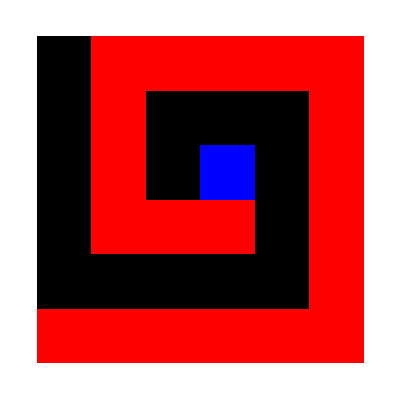

```mathematica
spiralcolors={0->Blue,1->Red,2->Black};
spiralimage={
{2,1,1,1,1,1},
{2,1,2,2,2,1},
{2,1,2,0,2,1},
{2,1,1,1,2,1},
{2,2,2,2,2,1},
{1,1,1,1,1,1}    };
ArrayPlot[spiralimage,ColorRules->spiralcolors]
```

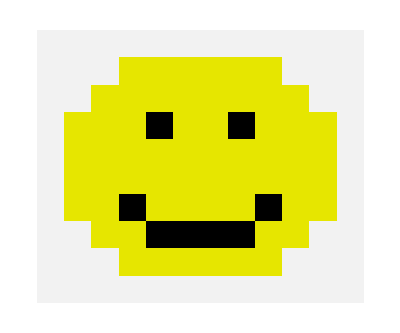

```mathematica
smileycolors={0->GrayLevel[0.95],1->RGBColor[.9,.9,0],2->Black};
smileyimage=ArrayPad[{
{0,0,1,1,1,1,1,1,0,0},
{0,1,1,1,1,1,1,1,1,0},
{1,1,1,2,1,1,2,1,1,1},
{1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1},
{1,1,2,1,1,1,1,2,1,1},
{0,1,1,2,2,2,2,1,1,0},
{0,0,1,1,1,1,1,1,0,0}    },1];
ArrayPlot[smileyimage,ColorRules->smileycolors]
```

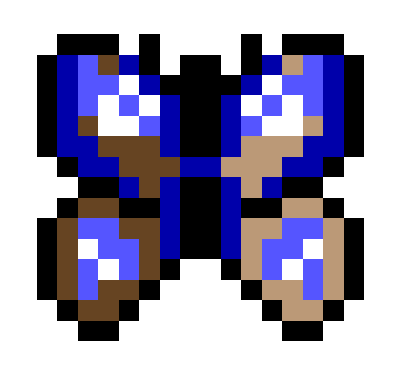

```mathematica
butterflycolors={0->White,1->Black,2->Darker[Blue],3->Lighter[Blue],4->Darker[Brown],5->Lighter[Brown]};
butterflyimage={
{0,1,1,1,0,1,0,0,0,0,1,0,1,1,1,0},
{1,2,3,4,2,1,0,1,1,0,1,2,5,3,2,1},
{1,2,3,3,0,2,1,1,1,1,2,0,3,3,2,1},
{1,2,3,0,3,0,2,1,1,2,0,3,0,3,2,1},
{1,2,4,0,0,3,2,1,1,2,3,0,0,5,2,1},
{1,2,2,4,4,4,2,1,1,2,5,5,5,2,2,1},
{0,1,2,2,4,4,4,2,2,5,5,5,2,2,1,0},
{0,0,1,1,2,4,2,1,1,2,5,2,1,1,0,0},
{0,1,4,4,1,1,2,1,1,2,1,1,5,5,1,0},
{1,4,3,3,4,4,2,1,1,2,5,5,3,3,5,1},
{1,4,0,3,3,4,2,1,1,2,5,3,3,0,5,1},
{1,4,3,0,3,4,1,0,0,1,5,3,0,3,5,1},
{1,4,3,4,4,1,0,0,0,0,1,5,5,3,5,1},
{0,1,4,4,1,0,0,0,0,0,0,1,5,5,1,0},
{0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0}       };
ArrayPlot[butterflyimage,ColorRules->butterflycolors]
```

We will show that with a number of reactions linearly proportional to the number of pixels, a surface CRN can grow a “uniquely addressed” structure.

Interpretation of species:
	P[i,j] appears at pixel i,j -- uniquely addressed, fully computed, this pixel is done and no longer needs to talk to neighbors
	T[i,j] tests for pixel i,j -- uniquely addressed, but might not appear in the correct location initially; only when it sees another specific test can it conclude correctness
	G[i,j] is growing a pixel -- the tests have verified, so uniquely addressed growth pixels are sure of their location
	A[i,j] is ready to add to the growth -- it is about to send out a test molecule
	B[i,j] is pending addition -- it has sent out a test molecule, which may need to be re-adsorbed, or which may succeed from test to confirmed growth
	C[i,j] is like A[i,j] but for orthogonal growth
	D[i,j] is like B[i,j] but for orthogonal growth
	color[c] forgets its uniquely-addressed location and leaves in its place just the intended color for that location

Warning : below, C is C \[N u l l] and D is D \[N u l l].  They look the same, but don’t have built-in rules associated with them.

```mathematica
UniquelyAddressedShapeCRN[image_]:=Module[{n=Length[image],m=Length[First[image]],species={},reactions={}},
Flatten[Join[
{rxno[S+EMPTY,A[0,0]+A[0,1],1]},  (* will define a random orientation *)

(* build a uniquely-addressed 2-pixel-wide line *)
Table[{
rxno[A[i,0]+EMPTY,B[i,0]+T[i+1,0],1],(* send out a test molecule *)
rxno[B[i,0]+T[i+1,0],A[i,0]+EMPTY,1],(* re-absorb a failed test *)
rxno[A[i,1]+EMPTY,B[i,1]+T[i+1,1],1],(* ditto *)
rxno[B [i,1]+T[i+1,1],A[i,1]+EMPTY,1],
rxno[T[i+1,0]+T[i+1,1],G[i+1,0]+G[i+1,1],1], (* adjacent test must be positioned correctly; proceed to growth *)
rxno[B[i,0]+G[i+1,0],P[i,0]+A[i+1,0],1], (* inform previous pixel that growth has been initiated; previous pixel is done *)
rxno[B[i,1]+G[i+1,1],C[i,1]+A[i+1,1],1] (* ditto, but on row 1 the previous must continue to orthogonal growth *)
},{i,0,n-2}],
{rxno[A[n-1,1],C[n-1,1],1]},(* last position of row 1 stops growing and must continue to orthogonal growth *)
{rxno[A[n-1,0],P[n-1,0],1]}, (* last position of row 0 stops growing and just finalizes the pixel *)

(* build an orthogonal uniquely-addressed 2-pixel-wide line. *)
Table[{
rxno[C[0,j]+EMPTY,D[0,j]+T[0,j+1],1],(* like the original line, but will be in orthogonal direction *)
rxno[D[0,j]+T[0,j+1],C[0,j]+EMPTY,1],
rxno[C[1,j]+EMPTY,D[1,j]+T[1,j+1],1],
rxno[D[1,j]+T[1,j+1],C[1,j]+EMPTY,1],
rxno[T[0,j+1]+T[1,j+1],G[0,j+1]+G[1,j+1],1],
rxno[D[0,j]+G[0,j+1],P[0,j]+C[0,j+1],1], (* on column 0, proceed to test for orthogonal growth *)
rxno[D[1,j]+G[1,j+1],P[1,j]+D[1,j+1],1] (* on column 1, wait to initiate filling-in reactions *)
},{j,1,m-2}],

(* fill the interior *)
Table[{
rxno[C[i,j]+EMPTY,P[i,j]+A[i,j+1],1], (* in column 2 or higher, if a non-edge cell reaches state C, it's on a flat facet *)
rxno[D[i-1,j+1]+A[i,j+1],C[i-1,j+1]+D[i,j+1],1] (* with A site ready to grow, releease D site to grow orthogonally *)
},{i,2,n-2},{j,1,m-2}],

(* handle the end-of-line issues *)
Table[{
rxno[D[n-2,j]+EMPTY,A[n-2,j]+T[n-1,j],1], (* when growing into the last column, "up" and "over" can be confused: do a test *)
rxno[A[n-2,j]+T[n-1,j],D[n-2,j]+EMPTY,1],
rxno[C[n-1,j-1]+T[n-1,j],P[n-1,j-1]+D[n-1,j],1], (* the last column only moves up after seeing a test *)
rxno[A[n-2,j]+D[n-1,j],C[n-2,j]+C[n-1,j],1] (* penultimate column must receive confirmation of test having been acted on *)
},{j,2,m-1}],
Table[rxno[C[i,m-1],P[i,m-1],1],{i,0,n-1}],  (* "top" row can convert to known pixels without waiting for further growth *)

(* convert each uniquely-addressed pixel into its designated color *)
Table[rxno[P[i,j],color[image[[i+1,j+1]]],1],{i,0,n-1},{j,0,m-1}]
]]
]
```

```mathematica
UniquelyAddressedShapeColors[colorrules_]:={
EMPTY->White,
P[_,_]->Pink,
T[_,_]->Lighter[Green],
G[_,_]->Darker[Green],
A[_,_]->Darker[Gray],
B[_,_]->Gray,
C[_,_]->Lighter[Gray],
D[_,_]->Lighter[Lighter[Gray]],
color[c_]:>(c/.colorrules)
}
UniquelyAddressedShapeField[image_]:=With[{size=Max[Length[image],Length[First[image]]]+3},
Table[If[{i,j}=={0,0},S,EMPTY],{i,-size,size},{j,-size,size}]]
```

```mathematica
Dynamic[ArrayPlot[surface,ColorRules->coloring,PlotLabel->time]]
```

```mathematica
(* should be done within 200 "seconds" *)
crn=spiralcrn=UniquelyAddressedShapeCRN[spiralimage];
surface=spiralsurface=UniquelyAddressedShapeField[spiralimage];
coloring=spiralcoloring=UniquelyAddressedShapeColors[spiralcolors];
time=0;While[!HaltedSurfaceCRNQ[crn,surface],surface=RunSurfaceCRN[crn,surface,1];time+=1]
```

```mathematica
(* should be done within 300 "seconds" *)
crn=smileycrn=UniquelyAddressedShapeCRN[smileyimage];
surface=smileysurface=UniquelyAddressedShapeField[smileyimage];
coloring=smilelycoloring=UniquelyAddressedShapeColors[smileycolors];
time=0;While[!HaltedSurfaceCRNQ[crn,surface],surface=RunSurfaceCRN[crn,surface,1];time+=1]
```

```mathematica
(* should be done within 400 "seconds" *)
crn=butterflycrn=UniquelyAddressedShapeCRN[butterflyimage];
surface=butterflysurface=UniquelyAddressedShapeField[butterflyimage];
coloring=butterflycoloring=UniquelyAddressedShapeColors[butterflycolors];
time=0;While[!HaltedSurfaceCRNQ[crn,surface],surface=RunSurfaceCRN[crn,surface,1];time+=1]
```

The surface CRNs contain about 4 times as many reactions as pixels -- i.e. it’s roughly linear -- so there is no algorithmic compression going on.  Alas.

```mathematica
{Length[spiralcrn],Times@@Dimensions[spiralimage]}
```

{148,36}

```mathematica
{Length[smileycrn],Times@@Dimensions[smileyimage]}
```

{446,120}

```mathematica
{Length[butterflycrn],Times@@Dimensions[butterflyimage]}
```

{846,240}

And let’s compile to watch the growth be a little faster.

```mathematica
{cButterCRN,cButterState}=CompileSurfaceCRN[butterflycrn,butterflysurface];cTime=0;
```

```mathematica
Dynamic[ShowSurfaceCRNState[cButterState,butterflycoloring,PlotLabel->cTime]]
```

```mathematica
halted=False;While[!halted,{{dt,devents,halted},cButterState}=InfoRunSurfaceCRN[cButterCRN,cButterState,1];cTime+=1]
```